## Solve the equation for y(t)

Solve the differential rotation equation for y(t):

```mathematica
f[t_,y_,α_,B_,s_]:=s t (1-α (s y+√(1-s^2)√(1-t^2-y^2))^2)-B;
```

```mathematica
Solve[f[t,y,α,B,s]==0,y]
```

{{y→-√(1-s^2-t^2+s^2 t^2-1/α+(2 s^2)/α+B/(s t α)-(2 B s)/(t α)-(2 √(s^4 (-1+s^2) t^2 α^2 (B^2-2 B s t+s^2 t^2+B s t α-s^2 t^2 α-B s t^3 α+s^2 t^4 α)))/(s^2 t^2 α^2))},{y→√(1-s^2-t^2+s^2 t^2-1/α+(2 s^2)/α+B/(s t α)-(2 B s)/(t α)-(2 √(s^4 (-1+s^2) t^2 α^2 (B^2-2 B s t+s^2 t^2+B s t α-s^2 t^2 α-B s t^3 α+s^2 t^4 α)))/(s^2 t^2 α^2))},{y→-√(1-s^2-t^2+s^2 t^2-1/α+(2 s^2)/α+B/(s t α)-(2 B s)/(t α)+(2 √(s^4 (-1+s^2) t^2 α^2 (B^2-2 B s t+s^2 t^2+B s t α-s^2 t^2 α-B s t^3 α+s^2 t^4 α)))/(s^2 t^2 α^2))},{y→√(1-s^2-t^2+s^2 t^2-1/α+(2 s^2)/α+B/(s t α)-(2 B s)/(t α)+(2 √(s^4 (-1+s^2) t^2 α^2 (B^2-2 B s t+s^2 t^2+B s t α-s^2 t^2 α-B s t^3 α+s^2 t^4 α)))/(s^2 t^2 α^2))}}

The four solutions are given by

y=±√(1-s^2-t^2+s^2 t^2-1/α+(2 s^2)/α+B/(s t α)-(2 B s)/(t α)±(2 √(s^4 (-1+s^2) t^2 α^2 (B^2-2 B s t+s^2 t^2+B s t α-s^2 t^2 α-B s t^3 α+s^2 t^4 α)))/(s^2 t^2 α^2))

Let’s simplify a bit of the math. Note that

```mathematica
FullSimplify[1-s^2-t^2+s^2 t^2==(1-s^2)(1-t^2)]
```

True

and

```mathematica
FullSimplify[s^4 (-1+s^2) t^2 α^2 (B^2-2 B s t+s^2 t^2+B s t α-s^2 t^2 α-B s t^3 α+s^2 t^4 α)==s^4 t^2(1-s^2) (B-s t) α^2 (s t^3 α+s t-s t α-B)]
```

True

so

y=±1/(√(α t))√(B/s-2 B s+α(1-s^2)(1-t^2)t-t+2 s^2 t±2 √((1-s^2) (B-s t) (s t^3 α+s t-s t α-B)))

```mathematica
y[t_,α_,B_,s_,S1_,S2_]:=S1 1/(√(α t))√(B/s-2 B s+α(1-s^2)(1-t^2)t-t+2 s^2 t+2 S2 √((1-s^2) (B-s t) (s t^3 α+s t-s t α-B)));
With[{s=0.3, α=0.3,B=0.1,t=0.4},
FullSimplify[
Evaluate[y/.Solve[f[t,y,α,B,s]==0,y][[1]]]
==
y[t,α,B,s,-1,-1]
]
]
```

True

These four curves form an asymmetric lemniscate, only half of which is visible on the observer’s side:

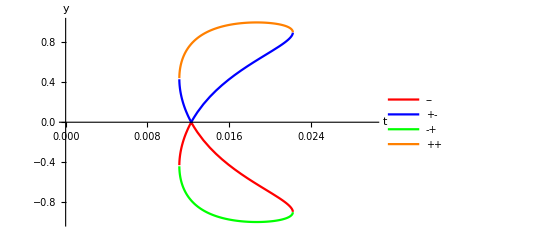

```mathematica
With[
{s=0.9, B=0.01, α=0.5},
Plot[
Evaluate@Table[
Table[
S1 1/(√(α t))√(B/s-2 B s+α(1-s^2)(1-t^2)t-t+2 s^2 t+ 2 S2 √((1-s^2) (B-s t) (s t^3 α+s t-s t α-B))),
{S1, -1, 1, 2}],
{S2, -1, 1, 2}],
{t,0, 0.03}, PlotStyle->{Red, Blue, Green, Orange}, PlotLegends->{"--","+-","-+","++"},
AxesLabel->{"t","y"}]
]
```

## Boundary 1

Let’s find the point where y = 0 from the (--) solution. There are three roots, only the first of which is real:

```mathematica
t/.Solve[y[t,α,B,s,-1,-1]==0,t][[1]]
```

-(2^(1/3) (-s+s α-s^3 α))/((-27 B s^2 α^2+54 B s^4 α^2-27 B s^6 α^2+√(108 (-s+s α-s^3 α)^3 (-s α+s^3 α)^3+(-27 B s^2 α^2+54 B s^4 α^2-27 B s^6 α^2)^2))^(1/3))+((-27 B s^2 α^2+54 B s^4 α^2-27 B s^6 α^2+√(108 (-s+s α-s^3 α)^3 (-s α+s^3 α)^3+(-27 B s^2 α^2+54 B s^4 α^2-27 B s^6 α^2)^2))^(1/3))/(3 2^(1/3) (-s α+s^3 α))

Simplify a bit:

```mathematica
FullSimplify[108 (-s+s α-s^3 α)^3 (-s α+s^3 α)^3+(-27 B s^2 α^2+54 B s^4 α^2-27 B s^6 α^2)^2 == 27 s^4 (1-s^2)^3 α^3 (27 B^2 (1-s^2) α-4 s^2 ((1-s^2) α-1)^3)]
```

True

```mathematica
FullSimplify[-27 B s^2 α^2+54 B s^4 α^2-27 B s^6 α^2==-27 B s^2 (1-s^2)^2 α^2]
```

True

Let

A_1=((s^2 (1-s^2)α)/2)^(1/3)(√(27  (1-s^2) α (27 B^2 (1-s^2) α-4 s^2 ((1-s^2) α-1)^3))-27 B  (1-s^2) α)^(1/3)

Then

t_1=(s(1- α+s^2 α))/A_1-A_1/(3 s α(1-s^2))

```mathematica
With[{s=0.3, α=0.1,B=0.1},
With[{A=((s^2 (1-s^2)α)/2)^(1/3)(√(27  (1-s^2) α (27 B^2 (1-s^2) α-4 s^2 ((1-s^2) α-1)^3))-27 B  (1-s^2) α)^(1/3)},
FullSimplify[
Evaluate[t/.Solve[y[t,α,B,s,-1,-1]==0,t][[1]]]==
(s(1- α+s^2 α))/A-A/(3 s α(1-s^2))
]]]
```

True

## Boundary 2

Let’s find the leftmost point of the lemniscate. There are different ways to do this, but one is to notice that this point coincides with the meeting point between the (++) and (+-) solutions. At this point, the inner square root in the equation for y(t) must be zero, so

```mathematica
Solve[(1-s^2) (B-s t) (s t^3 α+s t-s t α-B)==0,t][[1]]
```

{t→B/s}

t_2=B/s

## Boundary 3

Let’s find the rightmost point of the lemniscate. The same condition as above holds, but this time we keep the second root:

```mathematica
Solve[(1-s^2) (B-s t) (s t^3 α+s t-s t α-B)==0,t][[2]]
```

{t→-(2^(1/3) (-s+s α))/((-27 B s^2 α^2+√(729 B^2 s^4 α^4-108 s^3 α^3 (-s+s α)^3))^(1/3))-((-27 B s^2 α^2+√(729 B^2 s^4 α^4-108 s^3 α^3 (-s+s α)^3))^(1/3))/(3 2^(1/3) s α)}

```mathematica
FullSimplify[729 B^2 s^4 α^4-108 s^3 α^3 (-s+s α)^3==27 s^4 α^3 (4 s^2 (1-α)^3+27 B^2 α)]
```

True

Let

A_3=((√(27 s^4 α^3 (4 s^2 (1-α)^3+27 B^2 α))-27B s^2 α^2)/2)^(1/3)

Then

t_3=(s(1- α))/A_3-A_3/(3 s α)

```mathematica
With[{s=0.3, α=0.3,B=0.1},
With[{A=((√(27 s^4 α^3 (4 s^2 (1-α)^3+27 B^2 α))-27B s^2 α^2)/2)^(1/3)},
FullSimplify[
-(2^(1/3) (-s+s α))/((-27 B s^2 α^2+√(729 B^2 s^4 α^4-108 s^3 α^3 (-s+s α)^3))^(1/3))-((-27 B s^2 α^2+√(729 B^2 s^4 α^4-108 s^3 α^3 (-s+s α)^3))^(1/3))/(3 2^(1/3) s α)==
(s(1- α))/A-A/(3 s α)

]]]
```

True

## Boundaries 4 & 5

The final boundaries we need are where the lemniscate intersects the limb of the star. Since it’s symmetric about the equator, the top and bottom points of intersection occur at the same value of t. This happens when y^2+t^2=1, so we plug in y=√(1-t^2). Only the first solution here is real:

```mathematica
Solve[f[t,√(1-t^2),α,B,s]==0,t][[1]]
```

{t→-(2^(1/3) (s-s^3 α))/((27 B s^6 α^2+√(729 B^2 s^12 α^4+108 s^9 α^3 (s-s^3 α)^3))^(1/3))+((27 B s^6 α^2+√(729 B^2 s^12 α^4+108 s^9 α^3 (s-s^3 α)^3))^(1/3))/(3 2^(1/3) s^3 α)}

Let

A_45=((27 B s^6 α^2+√(27 s^9 α^3 (27 B^2 s^3 α+4 (s-s^3 α)^3)))/2)^(1/3)

Then

t_45=-(s(1-s^2 α))/A_45+A_45/(3 s^3 α)

```mathematica
With[{s=0.3, α=0.3,B=0.1},
With[{A=((27 B s^6 α^2+√(27 s^9 α^3 (27 B^2 s^3 α+4 (s-s^3 α)^3)))/2)^(1/3)},
FullSimplify[
-(2^(1/3) (s-s^3 α))/((27 B s^6 α^2+√(729 B^2 s^12 α^4+108 s^9 α^3 (s-s^3 α)^3))^(1/3))+((27 B s^6 α^2+√(729 B^2 s^12 α^4+108 s^9 α^3 (s-s^3 α)^3))^(1/3))/(3 2^(1/3) s^3 α)==
-(s(1-s^2 α))/A+A/(3 s^3 α)

]]]
```

True

## Summary

Given

	B =doppler parameter = (1-ⅇ^ξ)/ω_eq
	s= sin of the inclination
	c = cos of the inclination
	α=linear differential rotation parameter

the integration path along constant B is given by the curve

	y=±1/(√(α t))√(B/s-2 B s+α c^2(1-t^2)t-t+2 s^2 t±2 c √((B-s t) (s t^3 α+s t-s t α-B)))

The integration boundaries are

	t_1=(s(1-c^2 α))/A_1-A_1/(3 s α c^2)
	t_2=B/s	
	t_3=(s(1- α))/A_3-A_3/(3 s α)	
	t_45=-(s(1-s^2 α))/A_45+A_45/(3 s^3 α)

where

	A_1=c((s^2 α)/2)^(1/3)(√(27  α (27 B^2 c^2 α+4 s^2 (1-c^2 α)^3))-27 B  c α)^(1/3)
	A_3=(1/2)^(1/3)(√(27 s^4 α^3 (4 s^2 (1-α)^3+27 B^2 α))-27B s^2 α^2)^(1/3)
	A_45=s^2(1/2)^(1/3)(√(27 α^3 (27 B^2 α+4 (1-s^2 α)^3))+27 B α^2)^(1/3)

Given

	B =doppler parameter = (1-ⅇ^ξ)/ω_eq
	s= sin of the inclination
	c = cos of the inclination
	α=linear differential rotation parameter

the integration path along constant B is given by the curve

	y=±1/(√(α t))√(B/s-2 B s+α c^2(1-t^2)t-t+2 s^2 t±2 c √((B-s t) (s t^3 α+s t-s t α-B)))

The integration boundaries are

	t_1=(1-c^2 α)/A_1-A_1/(3 c^2 α)
	t_2=B/s
	t_3=(1- α)/A_3-A_3/(3 α)
	t_45=-(1-s^2 α)/A_45+A_45/(3 s^2 α)

where

	A_1=c((α c)/(2 s))^(1/3)(√(27 α (27 B^2 α+4 s^2/c^2 (1-c^2 α)^3))-27 B α)^(1/3)
	A_3=(α/(2 s))^(1/3)(√(27 α (27 B^2 α+4 s^2 (1-α)^3))-27B α)^(1/3)
	A_45=s(α/2)^(1/3)(√(27 α (27 B^2 α+4 (1-s^2 α)^3))+27 B α)^(1/3)

Check :

```mathematica
With[{s=0.3, α=0.1,B=0.1, c=√(1-0.3^2)},
With[{A=c((α c)/(2 s))^(1/3)(√(27 α (27 B^2 α+4 s^2/c^2 (1-c^2 α)^3))-27 B α)^(1/3)},
FullSimplify[
Evaluate[t/.Solve[y[t,α,B,s,-1,-1]==0,t][[1]]]==
(1-c^2 α)/A-A/(3 c^2 α)
]]]
```

True

```mathematica
With[{s=0.3, α=0.3,B=0.1},
With[{A=(α/(2 s))^(1/3)(√(27 α (27 B^2 α+4 s^2 (1-α)^3))-27B α)^(1/3)},
FullSimplify[
-(2^(1/3) (-s+s α))/((-27 B s^2 α^2+√(729 B^2 s^4 α^4-108 s^3 α^3 (-s+s α)^3))^(1/3))-((-27 B s^2 α^2+√(729 B^2 s^4 α^4-108 s^3 α^3 (-s+s α)^3))^(1/3))/(3 2^(1/3) s α)==
(1- α)/A-A/(3 α)

]]]
```

True

```mathematica
With[{s=0.3, α=0.3,B=0.1},
With[{A=s(α/2)^(1/3)(√(27 α (27 B^2 α+4 (1-s^2 α)^3))+27 B α)^(1/3)},
FullSimplify[
-(2^(1/3) (s-s^3 α))/((27 B s^6 α^2+√(729 B^2 s^12 α^4+108 s^9 α^3 (s-s^3 α)^3))^(1/3))+((27 B s^6 α^2+√(729 B^2 s^12 α^4+108 s^9 α^3 (s-s^3 α)^3))^(1/3))/(3 2^(1/3) s^3 α)==
-(1-s^2 α)/A+A/(3 s^2 α)

]]]
```

True